-2.32593+2.52049 x

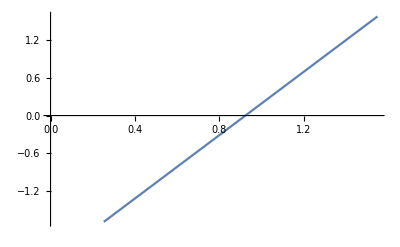

```mathematica
arr1={0.3, 0.348,0.396,0.444, 0.492, 0.54, 0.588, 0.636, 0.684, 0.732,0.78, 0.828, 0.876, 0.924, 0.972, 1.02,1.068,1.116,1.164,1.212,1.26,1.308,1.356,1.404,1.452,1.5};
arr2={-1.10525, -1.07996, -1.1225,-1.05986,-1.06783,-0.978257,-0.955469,-0.846209,-0.794931,-0.671395,-0.593028,-0.459459,-0.354877,-0.214726,-0.0844691,0.0593841,0.215,0.360097,0.540909,0.685119,0.891074,1.03252,1.26364,1.40065,1.65703,1.7881};
n=Length[arr1];funk={};
For[i=1,i≤n,i++,funk=Append[funk,{arr1[[i]],arr2[[i]]}]];
MatrixForm[funk];

rules=FindFit[funk,a+b*x,{a,b},x];y=a+b*x/. rules
g[x_]:=-2.3259256871794878+2.520485934472934 x
Plot[g[x],{x,0.252,1.548},AxesOrigin->{0,0}]
```

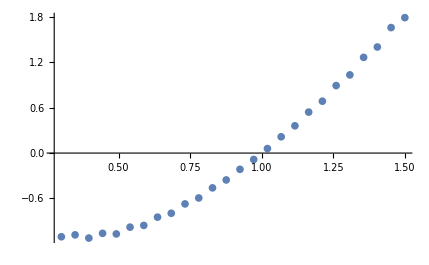
```mathematica
({{0.3, -1.10525}, {0.348, -1.07996}, {0.396, -1.1225}, {0.444, -1.05986}, {0.492, -1.06783}, {0.54, -0.978257}, {0.588, -0.955469}, {0.636, -0.846209}, {0.684, -0.794931}, {0.732, -0.671395}, {0.78, -0.593028}, {0.828, -0.459459}, {0.876, -0.354877}, {0.924, -0.214726}, {0.972, -0.0844691}, {1.02, 0.0593841}, {1.068, 0.215}, {1.116, 0.360097}, {1.164, 0.540909}, {1.212, 0.685119}, {1.26, 0.891074}, {1.308, 1.03252}, {1.356, 1.26364}, {1.404, 1.40065}, {1.452, 1.65703}, {1.5, 1.7881}});
ListPlot[funk]
-Graphics-;
```

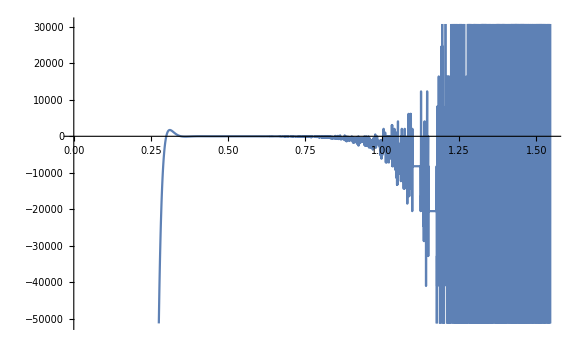

```mathematica
inpln:=InterpolatingPolynomial[funk,x];Collect[inpln,x];f[x_]:=-7.524199172381958*^10+2.57713246480314*^12 x-4.188311296076594*^13 x^2+4.299937177599049*^14 x^3-3.1321775419846655*^15 x^4+1.7235733740892938*^16 x^5-7.4483622785153*^16 x^6+2.5941218650870694*^17 x^7-7.414300450293256*^17 x^8+1.761556341572748*^18 x^9-3.5112063263108966*^18 x^10+5.908941362500788*^18 x^11-8.429833483988242*^18 x^12+1.021597759189182*^19 x^13-1.0519156707901133*^19 x^14+9.187624272859203*^18 x^15-6.782054545782033*^18 x^16+4.20602614983245*^18 x^17-2.1723279682784033*^18 x^18+9.22788735251155*^17 x^19-3.167583631823541*^17 x^20+8.56503219533247*^16 x^21-1.7556328697361016*^16 x^22+2.563192860985139*^15 x^23-2.374152551164155*^14 x^24+1.0483284654470762*^13 x^25
Plot[f[x],{x,0.252,1.548},AxesOrigin->{0,0}]
```

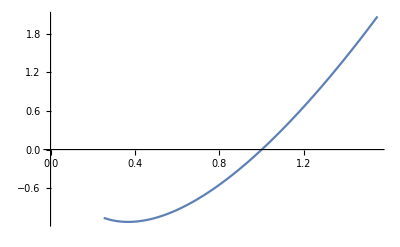

```mathematica
n=Length[arr1];funk1={};
For[i=1,i≤n,i+=2,funk1=Append[funk1,{arr1[[i]],arr2[[i]]}]];
MatrixForm[funk1]
({{0.3, -1.10525}, {0.396, -1.1225}, {0.492, -1.06783}, {0.588, -0.955469}, {0.684, -0.794931}, {0.78, -0.593028}, {0.876, -0.354877}, {0.972, -0.0844691}, {1.068, 0.215}, {1.164, 0.540909}, {1.26, 0.891074}, {1.356, 1.26364}, {1.452, 1.65703}})
inpln1:=InterpolatingPolynomial[funk1,x]
Collect[inpln1,x]
f1[x_]:=-0.02892690018160793-9.846764088904761 x+43.794182354191435 x^2-146.62318636895466 x^3+388.57319542465143 x^4-758.5707331668411 x^5+1084.1974546185008 x^6-1130.4680580940899 x^7+849.51780645953 x^8-447.82659506980724 x^9+157.07538399276922 x^10-32.9086974796021 x^11+3.114938356709965 x^12
Plot[f1[x],{x,0.252,1.548},AxesOrigin->{0,0}]
```

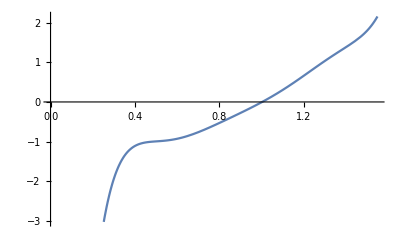

```mathematica
n=Length[arr1];funk2={};
For[i=3,i≤n,i+=3,funk2=Append[funk2,{arr1[[i]],arr2[[i]]}]];
MatrixForm[funk2]
({{0.396, -1.1225}, {0.54, -0.978257}, {0.684, -0.794931}, {0.828, -0.459459}, {0.972, -0.0844691}, {1.116, 0.360097}, {1.26, 0.891074}, {1.404, 1.40065}})
inpln2:=InterpolatingPolynomial[funk2,x]
Collect[inpln2,x]
f2[x_]:=-36.004449698481+309.6463594410931 x-1133.439985395276 x^2+2220.509042451546 x^3-2517.4825316897086 x^4+1659.9878702179935 x^5-591.118669881178 x^6+87.89661216764878 x^7
Plot[f2[x],{x,0.252,1.548},AxesOrigin->{0,0}]
```

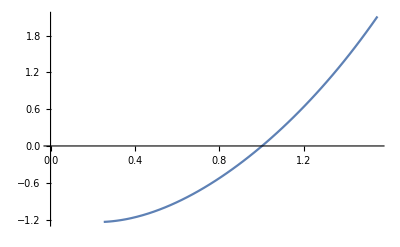

```mathematica
n=Length[arr1];funk3={};
For[i=5,i≤n,i+=5,funk3=Append[funk3,{arr1[[i]],arr2[[i]]}]];
MatrixForm[funk3]
({{0.492, -1.06783}, {0.732, -0.671395}, {0.972, -0.0844691}, {1.212, 0.685119}, {1.452, 1.65703}})
inpln3:=InterpolatingPolynomial[funk3,x]
Collect[inpln3,x]
f3[x_]:=-1.105487200370469-1.28778620359375 x+3.3147487709780092 x^2-1.2709306278935186 x^3+0.3452304165059158 x^4
Plot[f3[x],{x,0.252,1.548},AxesOrigin->{0,0}]
```

InterpolatingFunction[…]

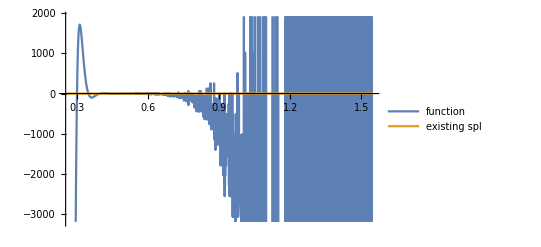

```mathematica
f[x_]:=-7.524199172381958*^10+2.57713246480314*^12 x-4.188311296076594*^13 x^2+4.299937177599049*^14 x^3-3.1321775419846655*^15 x^4+1.7235733740892938*^16 x^5-7.4483622785153*^16 x^6+2.5941218650870694*^17 x^7-7.414300450293256*^17 x^8+1.761556341572748*^18 x^9-3.5112063263108966*^18 x^10+5.908941362500788*^18 x^11-8.429833483988242*^18 x^12+1.021597759189182*^19 x^13-1.0519156707901133*^19 x^14+9.187624272859203*^18 x^15-6.782054545782033*^18 x^16+4.20602614983245*^18 x^17-2.1723279682784033*^18 x^18+9.22788735251155*^17 x^19-3.167583631823541*^17 x^20+8.56503219533247*^16 x^21-1.7556328697361016*^16 x^22+2.563192860985139*^15 x^23-2.374152551164155*^14 x^24+1.0483284654470762*^13 x^25


sp=Interpolation[funk,Method->"Spline"]
Plot[{f[x],sp[x]},{x,0.252,1.548},PlotLegends->{"function", "existing spl"}]
```